# Leads connected to 1 - 10 and 41 to 50

# a1 and a3

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
leads[10]
```

{1}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+301]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

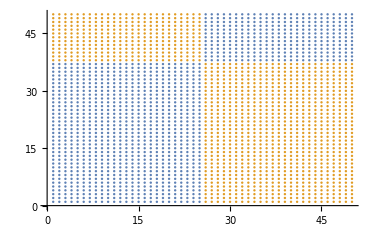

```mathematica
ListPlot[{Join[s[1,25,1,37],s[26,50,38,50]],Join[s[1,25,38,50],s[26,50,1,37]]}]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[Join[RandomSample[Join[s[1,25,1,37],s[26,50,38,50]],concentration],RandomSample[Join[s[1,25,38,50],s[26,50,1,37]],50-concentration]],First],1000]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,41,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[41;;50,41;;50]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
device1[1][[1,1]]
```

0.376543-0.675031 ⅈ

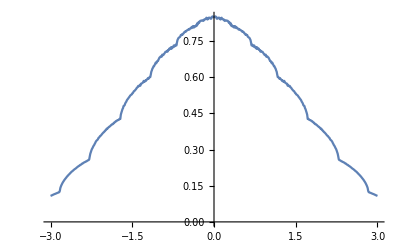

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,10][[10,10]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
Table[Export["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,conc,n],{n,500}]]},{ω,Range[0,3,0.01]}]],{conc,5,45,5}]
```

5

10

15

20

25

30

35

40

45

{/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_5_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_10_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_15_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_20_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_25_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_30_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_35_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_40_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_45_.dat}

```mathematica
transmission = Table[{x,Import["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2/ϵ1_conc_diag_"<>ToString[x]<>"_.dat"]},{x,5,45,5}]
```

{{5,{{0.,5.30376},{0.01,4.66997},{0.02,4.17998},{0.03,3.9234},{0.04,3.6035},{0.05,3.28939},{0.06,2.8661},{0.07,2.51001},{0.08,4.00541},{0.09,2.81741},{0.1,2.99612},{0.11,3.42295},{0.12,3.69084},{0.13,3.97735},{0.14,4.11494},272,{2.87,1.06875},{2.88,1.14489},{2.89,1.07832},{2.9,0.966785},{2.91,1.1465},{2.92,1.16986},{2.93,1.20011},{2.94,1.09322},{2.95,1.08505},{2.96,1.18201},{2.97,1.24538},{2.98,1.33346},{2.99,1.29604},{3.,1.25745}}},7,{45,{1}}}
 |  |  |  |

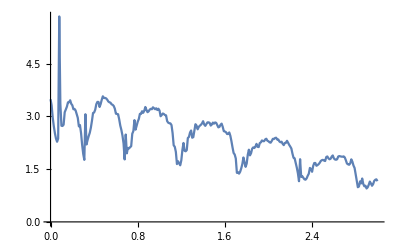

```mathematica
ListLinePlot[transmission[[4,2]]]
```

```mathematica
input =Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,20,n]},{ω,Range[0,3,0.01]}],{n,110,120}]
```

{{{0.,1.13671},{0.01,0.727167},{0.02,2.46402},{0.03,3.76117},{0.04,2.39802},{0.05,1.03466},{0.06,4.03183},{0.07,4.95861},{0.08,16.9363},{0.09,5.47743},{0.1,3.78651},{0.11,7.2591},{0.12,1.12981},{0.13,1.94825},{0.14,4.41206},272,{2.87,1.45898},{2.88,0.78744},{2.89,1.05859},{2.9,0.33183},{2.91,0.54357},{2.92,0.327096},{2.93,0.817847},{2.94,0.825435},{2.95,0.409793},{2.96,1.51178},{2.97,1.0876},{2.98,1.64746},{2.99,1.59093},{3.,1.40299}},9,{1}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{9,2}

```mathematica
Clear[misfit2]
```

```mathematica
misfit2[x_,y_,n_]:=misfit2[x,y,n]=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],250*Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,9}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{(*Transpose[*)ρ1(*][[2]]*),lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
misfit[x_,y_,n_]:=misfit[x,y,n]=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],1000*Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,9}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{(*Transpose[*)ρ1(*][[2]]*),lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
d1[x_,n_]:=Mean[Table[misfit2[x,y,n][[2]][[1]],{y,0.15,x-0.01,0.02}]]
```

```mathematica
Monitor[Table[Mean[Table[d1[x,n],{x,Range[0.5,2,0.05]}]],{n,10}],n]//N
```

{21.7879,16.6375,17.8919,23.5998,18.9789,19.1274,21.7948,19.2724,17.0662,14.5264}

```mathematica
d2[x_,n_]:=Mean[Table[misfit2[x,y,n][[1]],{y,0.15,x-0.01,0.02}]]
```

```mathematica
Monitor[Table[Mean[Table[d2[x,n],{x,Range[0.5,2,0.05]}]],{n,10}],n]//N
```

{{{5.,1.5537},{10.,1.34823},{15.,1.23272},{20.,1.21228},{25.,1.2147},{30.,1.27723},{35.,1.35923},{40.,1.44056},{45.,1.61869}},{{5.,1.37436},{10.,1.21354},{15.,1.14434},{20.,1.11525},{25.,1.14596},{30.,1.21822},{35.,1.30655},{40.,1.46907},{45.,1.58658}},{{5.,1.21115},{10.,1.13104},{15.,1.09395},{20.,1.1235},{25.,1.19537},{30.,1.29935},{35.,1.49565},{40.,1.64542},{45.,1.81257}},{{5.,1.4909},{10.,1.30327},{15.,1.23322},{20.,1.20412},{25.,1.16927},{30.,1.21219},{35.,1.33224},{40.,1.46599},{45.,1.59709}},{{5.,2.36206},{10.,2.21286},{15.,2.05931},{20.,2.00836},{25.,2.0376},{30.,2.08516},{35.,2.11491},{40.,2.21663},{45.,2.32996}},{{5.,1.76655},{10.,1.60909},{15.,1.51994},{20.,1.55013},{25.,1.55142},{30.,1.64649},{35.,1.73062},{40.,1.83988},{45.,1.979}},{{5.,1.48532},{10.,1.28785},{15.,1.22368},{20.,1.18454},{25.,1.20005},{30.,1.26367},{35.,1.36976},{40.,1.47699},{45.,1.63738}},{{5.,1.38435},{10.,1.27498},{15.,1.24387},{20.,1.24801},{25.,1.28144},{30.,1.375},{35.,1.51973},{40.,1.68248},{45.,1.8267}},{{5.,1.29242},{10.,1.17487},{15.,1.11466},{20.,1.15697},{25.,1.22082},{30.,1.32869},{35.,1.49358},{40.,1.6213},{45.,1.80529}},{{5.,1.17013},{10.,1.08082},{15.,1.06269},{20.,1.10197},{25.,1.17777},{30.,1.31614},{35.,1.47283},{40.,1.62447},{45.,1.81693}}}

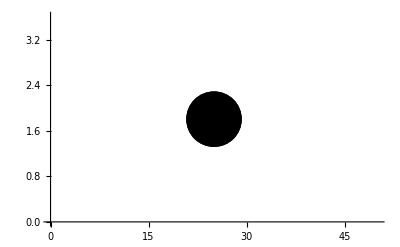

```mathematica
ListPlot[{%221[[2]][[5]]},PlotStyle->Directive[Black,PointSize[0.1]]]
```

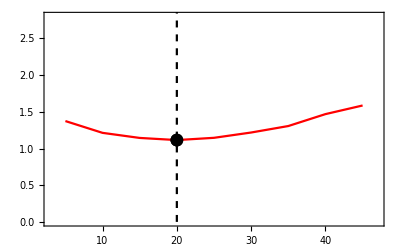

```mathematica
Show[ListLinePlot[{%257[[2]],Table[{20,x},{x,0,12.5}]},Frame->True,PlotStyle->{Red,Directive[Dashed,Black]}],ListPlot[{%257[[2]][[4]]},PlotStyle->Directive[Black,PointSize[0.023]]],PlotRange->{{3,47},{0,2.8}}]
```

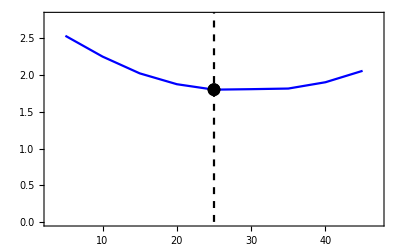

```mathematica
Show[ListLinePlot[{%221[[2]],Table[{25,x},{x,0,12.5}]},Frame->True,PlotStyle->{Blue,Directive[Dashed,Black]}],ListPlot[{%221[[2]][[5]]},PlotStyle->Directive[Black,PointSize[0.023]]],PlotRange->{{3,47},{0,2.8}}]
```

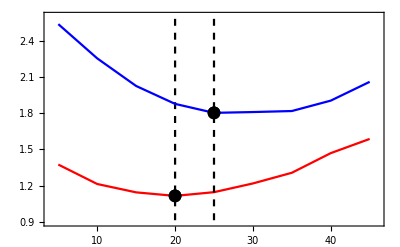

```mathematica
Show[%277,%278,PlotRange->{{4,46},{0.9,2.6}}]
```

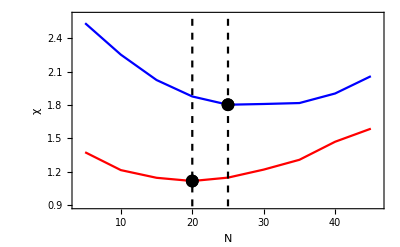

```mathematica
Show[%285,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

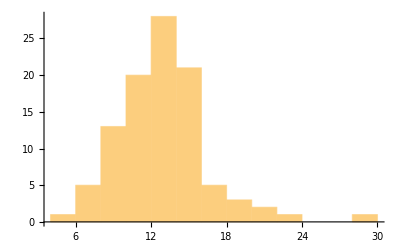

```mathematica
Histogram[%125]
```

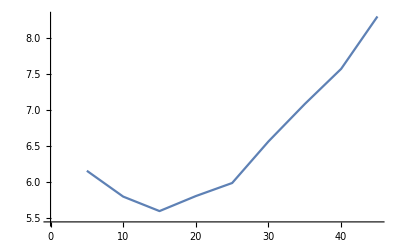

```mathematica
ListLinePlot[%114[[8]]]
```

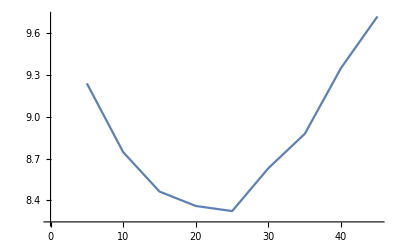
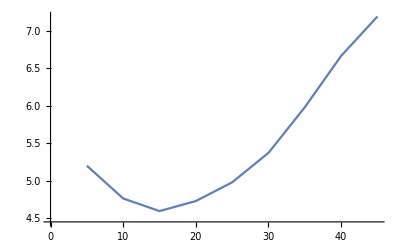
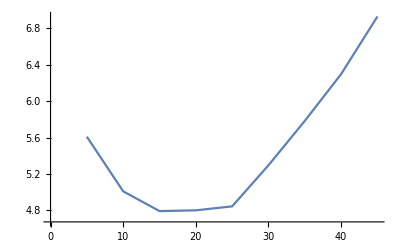
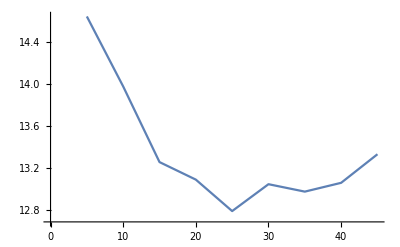
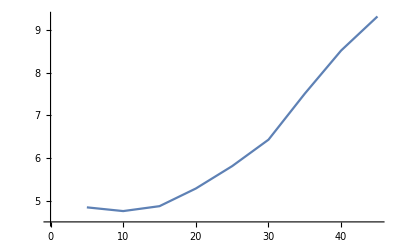
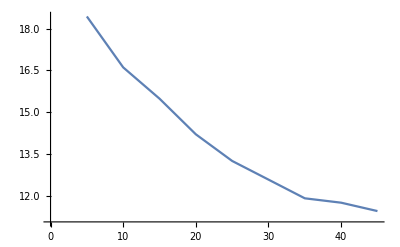
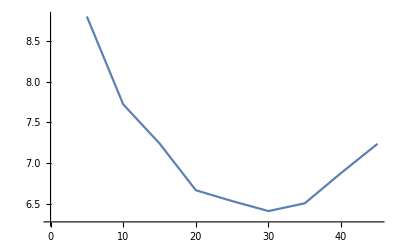
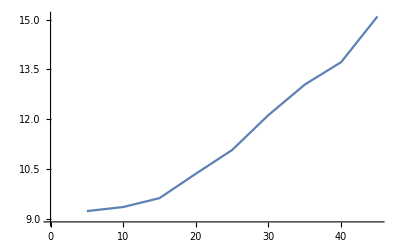
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
Table[{x,ListLinePlot[%114[[x]]]},{x,10}]
```

```mathematica
Table[ListPlot[d1[3,n],Joined->True],{n,10}]
```

```mathematica
d1[3,3][[7]]
```

{35,3.0428}

```mathematica
%94[[5]],
```

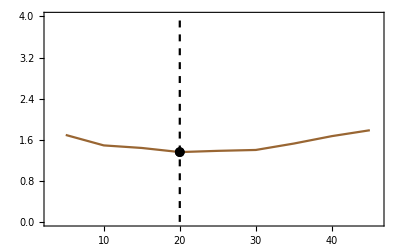

```mathematica
Show[ListLinePlot[{Mean[Table[d1[x,4],{x,Range[0.5,2,0.05]}]],Table[{20,y},{y,Range[0,8,0.01]}]},Frame->True,PlotStyle->{Brown,Directive[Black,Dashed]},PlotRange->{{3,46},{0,4}}],ListPlot[{ Mean[Table[d1[x,4],{x,Range[0.5,2,0.05]}]][[4]]},PlotMarkers-> {Automatic,Medium},PlotStyle->Black]]
```

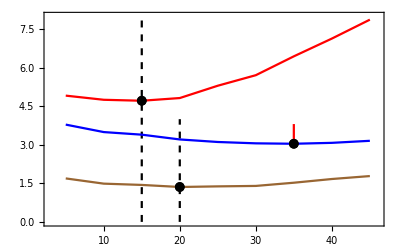

```mathematica
Show[%172,%176,%84,PlotRange->{{3,46},{0,8}}]
```

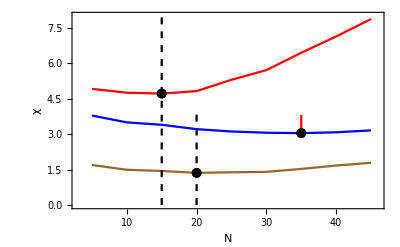

```mathematica
Show[%178,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

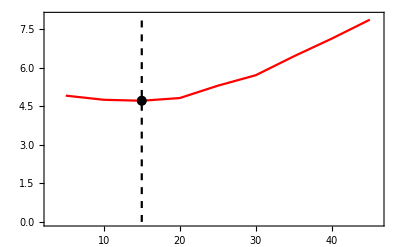

```mathematica
Show[ListLinePlot[{%94[[5]],Table[{15,y},{y,Range[0,8,0.01]}]},Frame->True,PlotStyle->{Red,Directive[Black,Dashed]},PlotRange->{{3,46},{0,8}}],ListPlot[{ %94[[5]][[3]]},PlotMarkers-> {Automatic,Medium},PlotStyle->Black]]
```

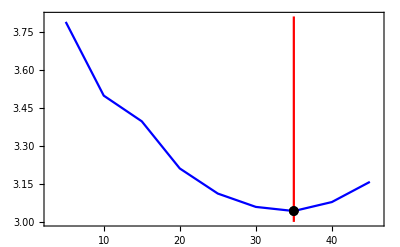

```mathematica
Show[ListLinePlot[{d1[3,3],Table[{35,y},{y,Range[2.99,3.9,0.01]}]},Frame->True,PlotStyle->{Blue,Red},PlotRange->{{3,46},{3,3.81}}],ListPlot[{d1[3,3][[7]]},PlotMarkers-> {Automatic,Medium},PlotStyle->Black]]
```

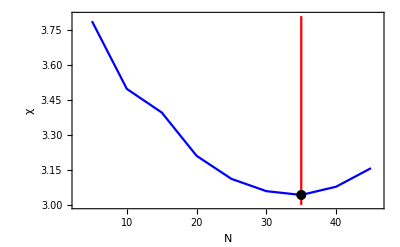

```mathematica
Show[%83,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]}]
```

```mathematica
Mean[Table[Print[nnn];Mean[Table[Mean[Table[misfit[xx,yy,nnn],{yy,Range[0.15+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]]
```

```mathematica
b[Y_,n_]:=b[Y,n]=Table[misfit[X+Y,X,n][[2]][[1]],{X,Range[0.15,3-Y,0.02]}]
```

```mathematica
Transpose[Join[{Range[1,100,1]},{Abs[Table[N[Mean[Abs[Flatten[Table[b[Y,n],{Y,Range[0.01,2,0.1]}]]]]],{n,100}]]}]]
```

{{1,23.7749},{2,17.9319},{3,17.6859},{4,17.6021},{5,19.0969},{6,20.7408},{7,38.8743},{8,21.1178},{9,26.1361},{10,23.7801},{11,31.8979},{12,18.4346},{13,9.65707},{14,19.9686},{15,21.3953},{16,33.8168},{17,23.733},{18,28.6649},{19,20.9293},{20,17.534},{21,15.5157},{22,16.0105},{23,34.5236},{24,18.0497},{25,37.4948},{26,27.0105},{27,25.7487},{28,25.7827},{29,25.9084},{30,21.0419},{31,30.4084},{32,21.8403},{33,21.2068},{34,17.8586},{35,20.0654},{36,36.9293},{37,19.1126},{38,26.2775},{39,22.9686},{40,19.3429},{41,19.2932},{42,15.856},{43,24.5471},{44,29.4476},{45,19.6859},{46,31.6283},{47,24.9921},{48,32.5759},{49,21.2592},{50,18.7094},{51,28.3717},{52,25.0864},{53,24.1152},{54,15.5602},{55,32.4686},{56,28.6283},{57,20.7147},{58,22.3351},{59,25.1414},{60,18.6649},{61,29.3508},{62,23.1937},{63,34.0262},{64,20.178},{65,31.2016},{66,20.7723},{67,28.7042},{68,20.5602},{69,15.8901},{70,39.1623},{71,18.5105},{72,19.0288},{73,18.4581},{74,25.3639},{75,30.377},{76,28.5524},{77,30.2461},{78,16.8796},{79,23.5864},{80,32.7853},{81,28.9162},{82,30.5},{83,28.2356},{84,17.555},{85,21.7251},{86,15.6257},{87,10.3194},{88,23.3927},{89,24.6073},{90,26.1518},{91,24.0759},{92,36.3639},{93,23.2618},{94,31.8115},{95,31.8848},{96,18.0052},{97,34.7565},{98,18.8901},{99,14.7513},{100,33.8246}}

```mathematica
Transpose[Join[{Range[1,100,1]},{Abs[Table[N[Mean[Abs[Flatten[Table[b[Y,n],{Y,Range[0.01,2,0.1]}]]]]],{n,100}]-25]/25}]]
```

{{1,0.0490052},{2,0.282723},{3,0.292565},{4,0.295916},{5,0.236126},{6,0.170366},{7,0.554974},{8,0.155288},{9,0.045445},{10,0.0487958},{11,0.275916},{12,0.262618},{13,0.613717},{14,0.201257},{15,0.144188},{16,0.35267},{17,0.0506806},{18,0.146597},{19,0.162827},{20,0.298639},{21,0.379372},{22,0.359581},{23,0.380942},{24,0.27801},{25,0.499791},{26,0.0804188},{27,0.0299476},{28,0.0313089},{29,0.0363351},{30,0.158325},{31,0.216335},{32,0.126387},{33,0.151728},{34,0.285654},{35,0.197382},{36,0.477173},{37,0.235497},{38,0.0510995},{39,0.0812565},{40,0.226283},{41,0.228272},{42,0.365759},{43,0.0181152},{44,0.177906},{45,0.212565},{46,0.265131},{47,0.000314136},{48,0.303037},{49,0.149634},{50,0.251623},{51,0.134869},{52,0.0034555},{53,0.0353927},{54,0.377592},{55,0.298743},{56,0.145131},{57,0.171414},{58,0.106597},{59,0.00565445},{60,0.253403},{61,0.174031},{62,0.0722513},{63,0.361047},{64,0.19288},{65,0.248063},{66,0.16911},{67,0.148168},{68,0.177592},{69,0.364398},{70,0.566492},{71,0.259581},{72,0.238848},{73,0.261675},{74,0.014555},{75,0.215079},{76,0.142094},{77,0.209843},{78,0.324817},{79,0.0565445},{80,0.311414},{81,0.156649},{82,0.22},{83,0.129424},{84,0.297801},{85,0.130995},{86,0.374974},{87,0.587225},{88,0.0642932},{89,0.0157068},{90,0.0460733},{91,0.0369634},{92,0.454555},{93,0.0695288},{94,0.272461},{95,0.275393},{96,0.279791},{97,0.390262},{98,0.244398},{99,0.409948},{100,0.352984}}

```mathematica
Show[Show[ListLinePlot[{tra50,MovingAverage[traa50,15]},PlotStyle->{Red,Directive[Dashed,Black]},PlotLegends->Placed[legend,{0.07,0.85}],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],Frame->True,ImageSize->{600,470},PlotRange->{{0.5,3},{0,45}}],b],FrameLabel->{{Text[Style[𝒯,30,FontFamily->"Times New Roman"]],None},{Text[Style["E/t",30,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",22,GrayLevel[0]},(*Epilog->{(*Dynamic[If[True,*)Locator[{2.37,32.3},D1,ImageSize->350](*{}]]*)},*)Epilog->{(*Dynamic[If[True,*)Locator[{2.37,32.3},Show[ListLinePlot[{misfit1,misfit2,Table[{50,x},{x,Range[3,6.3]}]},PlotStyle->{Blue,Red,Directive[Black,Dashed]},Frame->True,PlotRange->{{7,93},{3,6.2}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{Text[Style[χ,20,FontFamily->"Times New Roman"]],None},{Text[Style["N",20,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}],ListPlot[{misfit1[[5]],misfit2[[5]]},PlotStyle->Directive[Black,PointSize[0.02]]]],ImageSize->250](*{}]]*)}]
```

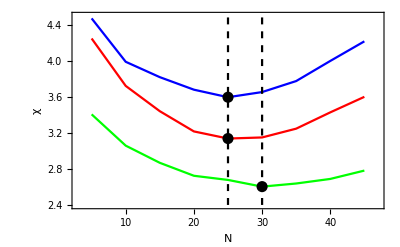

```mathematica
Show[ListPlot[{Transpose[Join[{Range[5,45,5]},{1000*%82[[88]]}]],Transpose[Join[{Range[5,45,5]},{1000*%82[[89]]}]],Table[{25,x},{x,Range[2,4.5,0.01]}],Table[{30,x},{x,Range[2,4.5,0.01]}],Transpose[Join[{Range[5,45,5]},{1000*%82[[31]]/2}]]},Joined->True,Frame->True,PlotStyle->{Red,Blue,Directive[Black,Dashed],Directive[Black,Dashed],Green},PlotRange->{{03,047},{2.4,4.5}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],Frame->True,FrameLabel->{{Text[Style[χ,20,FontFamily->"Times New Roman"]],None},{Text[Style["N",20,FontFamily->"Times New Roman"]],None}},LabelStyle->{FontFamily->"Times New Roman",17,GrayLevel[0]}],ListPlot[{Transpose[Join[{Range[5,45,5]},{1000*%82[[88]]}]][[5]],Transpose[Join[{Range[5,45,5]},{1000*%82[[89]]}]][[5]],Transpose[Join[{Range[5,45,5]},{1000*%82[[31]]/2}]][[6]]},PlotStyle->Directive[Black,PointSize[0.02]]]]
```

```mathematica
Export["~/PhD/quantum_sudoq/fig_2_b.pdf",%124]
```

~/PhD/quantum_sudoq/fig_2_b.pdf

```mathematica
Mean[%27]
```

0.217457

```mathematica
b1[Y_,n_]:=b1[Y,n]=Table[misfit[X+Y,X,n][[1]],{X,Range[0.15,3-Y,0.02]}]
```

```mathematica
Table[Print[n];Mean[Table[Mean[b1[y,n]],{y,Range[0.01,2,0.1]}]],{n,100}]
```

{{0.00595852,0.00561467,0.00538237,0.00531442,0.00529454,0.00532991,0.00559123,0.00576226,0.00599858},{0.00394148,0.00362252,0.00348011,0.00349816,0.00353029,0.00370626,0.00390568,0.00421641,0.00447345},{0.00439459,0.00406428,0.00399696,0.00398395,0.00401019,0.00417465,0.00442201,0.00465424,0.00505065},{0.00389567,0.0035958,0.00346589,0.00342465,0.00346547,0.00370586,0.003842,0.00414409,0.00445639},{0.00410677,0.00381172,0.00373563,0.0037786,0.00390266,0.00407923,0.0043474,0.00478027,0.00510369},{0.00331222,0.00298237,0.0028215,0.00271978,0.00281216,0.00295485,0.00318731,0.00341089,0.0037432},{0.005536,0.00479463,0.00430992,0.00395883,0.0036434,0.00346984,0.00330932,0.00328373,0.00331178},{0.00354212,0.00324394,0.00309476,0.00298702,0.00302199,0.00315614,0.00337573,0.00364758,0.00393845},{0.00464476,0.00418777,0.00392852,0.00375484,0.00367538,0.00375422,0.00383622,0.00391886,0.00417411},{0.00439685,0.00398353,0.0037331,0.00357539,0.00358212,0.00356951,0.00380414,0.00399569,0.00424094},{0.00885526,0.0085514,0.00811694,0.0080805,0.00794613,0.00799088,0.00817099,0.00828634,0.00841823},{0.00438217,0.00413756,0.00405327,0.00406105,0.00407229,0.00431747,0.00463511,0.00494898,0.00530166},{0.00325277,0.00319121,0.0032596,0.00343949,0.00372785,0.00413601,0.00451763,0.00497109,0.00548836},{0.00640356,0.00607927,0.00583717,0.00590703,0.00590939,0.00619428,0.00624998,0.00644168,0.00684773},{0.00409858,0.00370017,0.00348101,0.00330743,0.00332427,0.00334925,0.00357394,0.00379446,0.00408393},{0.00814105,0.00758637,0.00729848,0.00691822,0.00681395,0.006835,0.00677092,0.00688413,0.00692439},{0.00379155,0.00325156,0.00300753,0.00282448,0.00269848,0.00271418,0.00280788,0.00299589,0.00318146},{0.00538414,0.00491136,0.00467569,0.00458526,0.00458072,0.00456838,0.00473463,0.00500011,0.0051655},{0.00420731,0.00391987,0.00376778,0.00372683,0.00373479,0.0039373,0.00417096,0.00437506,0.00464422},{0.00414111,0.00390045,0.00387157,0.00382122,0.00388195,0.00405916,0.0043387,0.00463828,0.00493101},{0.00396784,0.00376285,0.00372468,0.00379419,0.00387742,0.00412623,0.00440862,0.0047692,0.00512001},{0.00356695,0.0033509,0.00321945,0.00324055,0.0032656,0.00354245,0.00376467,0.00403246,0.00442038},{0.00989245,0.00927991,0.00885033,0.00847595,0.00823521,0.00820589,0.00811822,0.0080164,0.00808908},{0.00648816,0.00622795,0.00611304,0.00619435,0.00628126,0.00658566,0.00663151,0.00686101,0.00726113},{0.0048592,0.00417467,0.00376228,0.00352635,0.00324047,0.0032026,0.00314615,0.00312766,0.00329628},{0.00437081,0.00395342,0.00381912,0.00374132,0.00378872,0.0038829,0.00403119,0.00427004,0.00463589},{0.00853407,0.0080924,0.00790685,0.00766475,0.00772544,0.0076679,0.00807381,0.00820461,0.00852965},{0.00728664,0.00682683,0.00651168,0.00643648,0.00641852,0.00646859,0.00656382,0.00665622,0.00693203},{0.00404618,0.00354134,0.00324045,0.0031398,0.00294832,0.00299488,0.00311412,0.00335163,0.00349322},{0.00691469,0.00659336,0.0063581,0.00646911,0.0064489,0.00660178,0.00701836,0.00721254,0.00754889},{0.00681519,0.00611886,0.0057369,0.00544883,0.00535614,0.00520727,0.00527683,0.0053785,0.00556416},{0.00897759,0.00852387,0.00836807,0.00810711,0.0081238,0.00820961,0.00811943,0.00843977,0.00864909},{0.00350665,0.00309705,0.00297664,0.00282945,0.00288261,0.00293513,0.00320057,0.00340245,0.00374992},{0.00363047,0.00328535,0.00313632,0.00309644,0.00311435,0.00328278,0.00348236,0.00375769,0.00407776},{0.00390963,0.00364853,0.00350264,0.0035457,0.00353232,0.00370947,0.00399067,0.00418591,0.00455022},{0.0104481,0.00960518,0.0091026,0.00854483,0.00832166,0.00809434,0.00790439,0.00807244,0.00800017},{0.00308116,0.00281206,0.00271548,0.00277389,0.00285703,0.00310848,0.00339159,0.00372035,0.00410214},{0.00489934,0.00451472,0.00431328,0.0042482,0.00420867,0.00434988,0.00448574,0.00461132,0.0049496},{0.00387179,0.0033874,0.0031131,0.00298628,0.00287136,0.00291531,0.00303397,0.00325864,0.00350625},{0.00370125,0.00333727,0.0032205,0.00315846,0.00324949,0.0033926,0.00362472,0.00383094,0.00417082},{0.00329309,0.0029812,0.00284526,0.00280676,0.00291252,0.00307726,0.00332287,0.00368315,0.00406457},{0.00572806,0.00542548,0.00531744,0.00530202,0.00538577,0.00548834,0.00572626,0.00607524,0.00637583},{0.00382122,0.00343957,0.00323574,0.00317491,0.00307351,0.00324983,0.003382,0.00361838,0.00383025},{0.00511274,0.00460529,0.00430182,0.00403236,0.00399418,0.00398655,0.00407539,0.00426503,0.00443167},{0.00507329,0.00460052,0.00430321,0.00411649,0.00406096,0.00411188,0.00420497,0.00442394,0.00472155},{0.00627452,0.00567699,0.00533955,0.0050984,0.00488897,0.00491514,0.0049077,0.00511039,0.00524705},{0.00430618,0.00382809,0.00352656,0.0034681,0.0033682,0.00346966,0.00356027,0.00368556,0.00399877},{0.00582366,0.00510666,0.00473342,0.00435878,0.00418398,0.0041067,0.0040586,0.00416786,0.00424564},{0.00342122,0.00316538,0.00302481,0.00306024,0.00318864,0.00334667,0.00356968,0.00390975,0.00424768},{0.00661623,0.00628894,0.00620705,0.00609871,0.00627376,0.00639728,0.00676103,0.00699175,0.00735965},{0.00627021,0.00570365,0.00544489,0.00514167,0.00500091,0.00488785,0.00495855,0.00505339,0.00516649},{0.00367524,0.0032983,0.00317354,0.00308035,0.0030811,0.00324881,0.00342285,0.00359098,0.00389902},{0.00477344,0.00452407,0.00450025,0.00449018,0.00456333,0.00486572,0.00500443,0.00523372,0.00570287},{0.0049625,0.00468621,0.00461708,0.00459957,0.00476963,0.00497977,0.00521459,0.00562123,0.0059384},{0.0113384,0.0106434,0.0101247,0.00993413,0.00962837,0.00945797,0.00943176,0.00953311,0.0096432},{0.00637934,0.00575944,0.00539255,0.005075,0.00497024,0.00484294,0.00498115,0.00512939,0.00528979},{0.004,0.00366674,0.0034632,0.00342954,0.00336208,0.00351608,0.00369522,0.00393363,0.00421743},{0.00526839,0.00485827,0.00464302,0.00446529,0.00448122,0.00459931,0.00472323,0.00498923,0.00527319},{0.00543418,0.00491339,0.00461374,0.00448862,0.00435282,0.00433571,0.00444144,0.00461848,0.00486565},{0.00384861,0.00363018,0.00363619,0.00371274,0.0038265,0.00404545,0.00440272,0.0047791,0.00521689},{0.0114162,0.010531,0.00999878,0.00941737,0.00926988,0.00909387,0.00883019,0.00878429,0.0088726},{0.00530471,0.00473983,0.00459445,0.00428341,0.00426567,0.00429248,0.0045326,0.00466062,0.0049674},{0.00987265,0.00910814,0.00869908,0.00821313,0.00792357,0.00774897,0.00753363,0.00762954,0.00761507},{0.00355874,0.00327223,0.0031279,0.00310521,0.00310962,0.00332599,0.00347691,0.00375929,0.00410415},{0.00696611,0.00637906,0.00596596,0.00572492,0.00561535,0.00562652,0.0056212,0.00559117,0.00582463},{0.00419794,0.00389037,0.00381109,0.0037802,0.003862,0.00403345,0.00426175,0.00458286,0.00493011},{0.00461977,0.00399958,0.00365014,0.00337677,0.00320645,0.00307219,0.00319618,0.00323995,0.00337966},{0.00486963,0.00442737,0.00417871,0.00414975,0.0040873,0.00414198,0.00432438,0.00458118,0.00486545},{0.00370964,0.00365251,0.00373438,0.00388777,0.00422895,0.00459841,0.00511694,0.00550095,0.00599082},{0.00904047,0.00816891,0.00752532,0.00696607,0.00667854,0.00639282,0.00610527,0.00607179,0.00604251},{0.00450839,0.0041504,0.00387839,0.00388403,0.00390576,0.00399466,0.00423839,0.00449721,0.00479908},{0.0121107,0.0116505,0.0115958,0.0112569,0.0115768,0.0115785,0.0117425,0.0120505,0.0123854},{0.00626824,0.00581489,0.00573255,0.00567944,0.00583125,0.00588941,0.00615934,0.00643632,0.00677068},{0.00381198,0.00323884,0.00296055,0.00275327,0.00263634,0.00268294,0.00275783,0.00289003,0.00309117},{0.00459499,0.00411107,0.00374974,0.00347299,0.00331507,0.00324229,0.00335586,0.00346723,0.00357351},{0.00498235,0.00438572,0.0040791,0.00382513,0.00370763,0.00366807,0.00369503,0.0038295,0.00405241},{0.00793958,0.00727211,0.00677081,0.00652554,0.00627705,0.00628903,0.00613987,0.00605146,0.00623135},{0.00480617,0.00454564,0.00443253,0.00446831,0.00450114,0.0047443,0.00493279,0.005317,0.00554171},{0.00413775,0.00370477,0.00353393,0.00344128,0.00341578,0.00354284,0.00373005,0.00393289,0.00424101},{0.00446444,0.00391771,0.00359197,0.00333476,0.00331796,0.00327863,0.00341021,0.0035161,0.00364988},{0.00538947,0.0047762,0.00449982,0.00428445,0.00407916,0.00404498,0.00409869,0.00420891,0.00431824},{0.00485918,0.0042819,0.00398928,0.00365188,0.00356233,0.00344879,0.00355537,0.00372425,0.00383493},{0.00574843,0.00518836,0.00483175,0.00446294,0.00438687,0.00431755,0.00441338,0.00456116,0.00465165},{0.00372756,0.00346892,0.00337093,0.00335299,0.00339298,0.00355435,0.00378703,0.00407541,0.00438577},{0.00595514,0.00540599,0.00511815,0.00500743,0.00494585,0.00491186,0.00504574,0.00528891,0.00547235},{0.00407043,0.00376749,0.00371587,0.00382398,0.00397156,0.00417301,0.0044762,0.00470845,0.0051416},{0.00476567,0.00468895,0.00484231,0.00497253,0.00529308,0.0056564,0.00599057,0.00659018,0.00707287},{0.00425127,0.00372382,0.00344261,0.00321763,0.00313848,0.00315062,0.00324845,0.00342959,0.00360231},{0.00447495,0.00399202,0.00382119,0.00368188,0.00359805,0.00365536,0.00377781,0.00400145,0.00421951},{0.00452671,0.00395444,0.00364605,0.00337912,0.00322152,0.00322331,0.00334928,0.00349082,0.00360897},{0.00441288,0.00392749,0.00372935,0.00346624,0.00347715,0.00348413,0.00368169,0.00385389,0.00412087},{0.00656563,0.00588286,0.00529064,0.00508627,0.00473986,0.00462156,0.0045439,0.00455921,0.00456882},{0.00462357,0.00422796,0.00402347,0.00388579,0.00387865,0.0039837,0.00414349,0.00434656,0.00466465},{0.00589175,0.00517545,0.00480397,0.00443868,0.00432919,0.00424685,0.00417212,0.00423152,0.00446903},{0.00628127,0.00557719,0.00514117,0.00476219,0.00458659,0.00441154,0.00445439,0.0044618,0.00453935},{0.00544636,0.00516128,0.0050637,0.00506868,0.00521091,0.00535174,0.0055492,0.00594887,0.00624373},{0.0154946,0.0146864,0.0141067,0.0133763,0.0131754,0.0128156,0.0125686,0.0124325,0.0123776},{0.00384834,0.00347858,0.00340316,0.0033322,0.00342994,0.0035932,0.00387601,0.00407817,0.00445009},{0.0040574,0.00376523,0.00375074,0.00376335,0.00390742,0.00409339,0.00438223,0.00477906,0.00514245},{0.00755269,0.00666671,0.00626213,0.00572201,0.00549986,0.00523563,0.00526684,0.00530833,0.00531468}}

```mathematica
Transpose[Join[{2*Range[5,45,5]},{1000*%26[[1]]}]]
```

{{10,5.95852},{20,5.61467},{30,5.38237},{40,5.31442},{50,5.29454},{60,5.32991},{70,5.59123},{80,5.76226},{90,5.99858}}

```mathematica
Export["~/PhD/quantum_sudoq/misfit_50_2.dat",Transpose[Join[{2*Range[5,45,5]},{1000*%26[[9]]}]]]
```

~/PhD/quantum_sudoq/misfit_50_2.dat

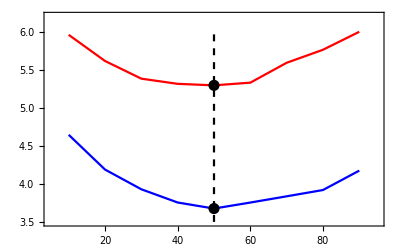

```mathematica
Show[ListPlot[{Transpose[Join[{2*Range[5,45,5]},{1000*%26[[1]]}]],Transpose[Join[{2*Range[5,45,5]},{1000*%26[[9]]}]],Table[{50,x},{x,Range[3.25,6,0.01]}]},Joined->True,Frame->True,PlotStyle->{Red,Blue,Directive[Black,Dashed]},PlotRange->{{5,95},{3.5,6.2}}],ListPlot[{Transpose[Join[{2*Range[5,45,5]},{1000*%26[[1]]}]][[5]],Transpose[Join[{2*Range[5,45,5]},{1000*%26[[9]]}]][[5]]},PlotStyle->Directive[Black,PointSize[0.02]]]]
```

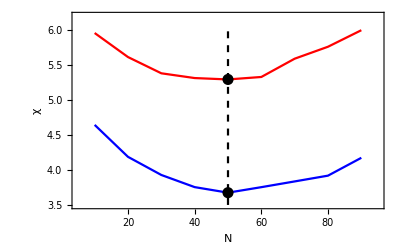

```mathematica
Show[%62,AxesLabel->{HoldForm[N],HoldForm[Χ]},FrameLabel->{{Text[Style[χ,30,FontFamily->"Times New Roman"]],None},{Text[Style[N,30,FontFamily->"Times New Roman"]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0]}]
```

```mathematica
Interpolation[%35]
```

InterpolatingFunction[…]

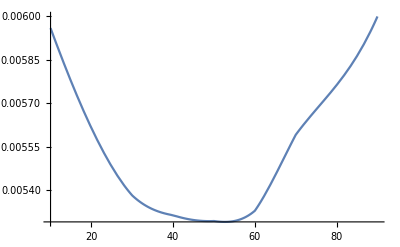

```mathematica
Plot[%36[x],{x,10.,90.}]
```

```mathematica
Plot[%31[x],{x,10.,90.},PlotRange->All]
```

-Graphics-

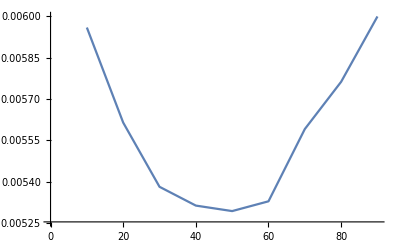

```mathematica
ListPlot[%29,Joined->True]
```

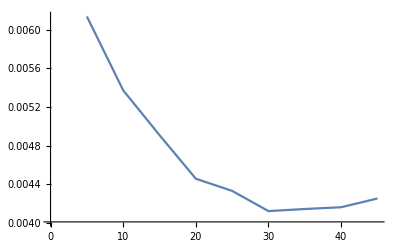
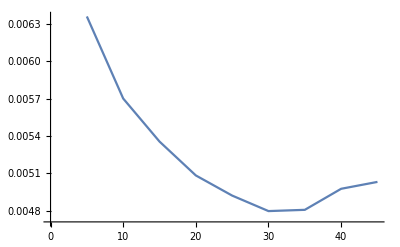
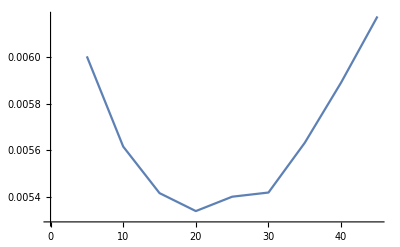
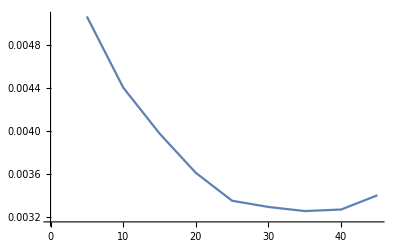
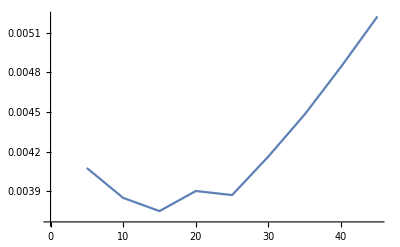
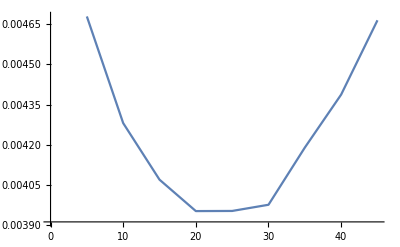
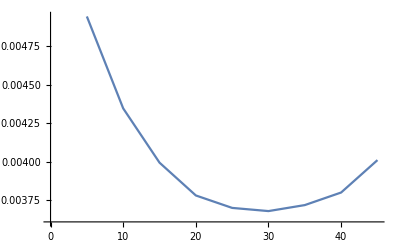
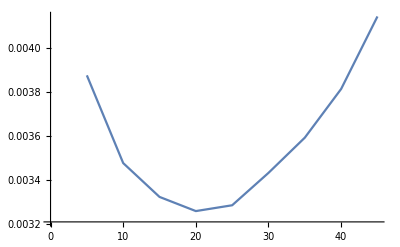
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-},{11,-Graphics-},{12,-Graphics-},{13,-Graphics-},{14,-Graphics-},{15,-Graphics-}}

```mathematica
Table[{n,ListPlot[Transpose[Join[{Range[5,45,5]},{%104[[n]]}]],Joined->True]},{n,15}]
```

```mathematica
Show[ListPlot[{Transpose[Join[{Range[5,45,5]},{1000*%92[[7]]}]],Transpose[Join[{Range[5,45,5]},{1000*%92[[10]]}]],Transpose[Join[{Range[5,45,5]},{1000*%92[[9]]}]],Table[{25,x},{x,Range[2,5,0.01]}],Table[{30,x},{x,Range[2,5,0.01]}](*,Transpose[Join[{2*Range[5,45,5]},{1000*%104[[11]]}]]*)},Joined->True,Frame->True,PlotStyle->{Red,Blue,Brown,Directive[Dashed,Black],Directive[Dashed,Black]},PlotRange->{{0,50},{2.5,5}}],ListPlot[{Transpose[Join[{Range[5,45,5]},{1000*%92[[7]]}]][[6]],Transpose[Join[{Range[5,45,5]},{1000*%92[[10]]}]][[5]],Transpose[Join[{Range[5,45,5]},{1000*%92[[9]]}]][[5]]},PlotStyle->Directive[Black,PointSize[0.02]]]]
```

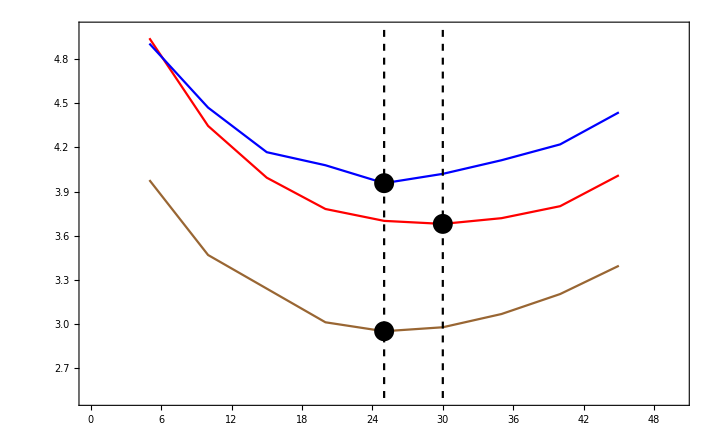

-Graphics-

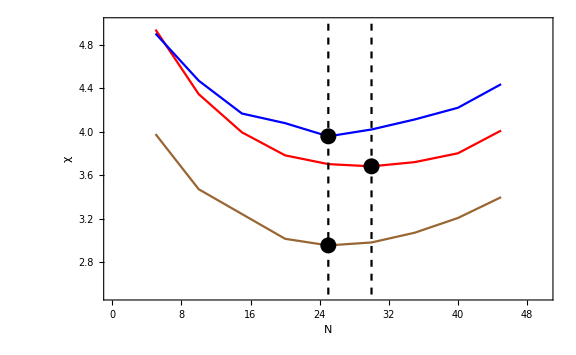

```mathematica
Show[%69,FrameLabel->{{Text[Style[χ,35,FontFamily->"Times New Roman"]],None},{Text[Style[N,35,FontFamily->"Times New Roman"]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0.1]},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],ImageSize->Large]
```

```mathematica
Export["~/PhD/quantum_sudoq/fig_2_b.pdf",%72]
```

~/PhD/quantum_sudoq/fig_2_b.pdf

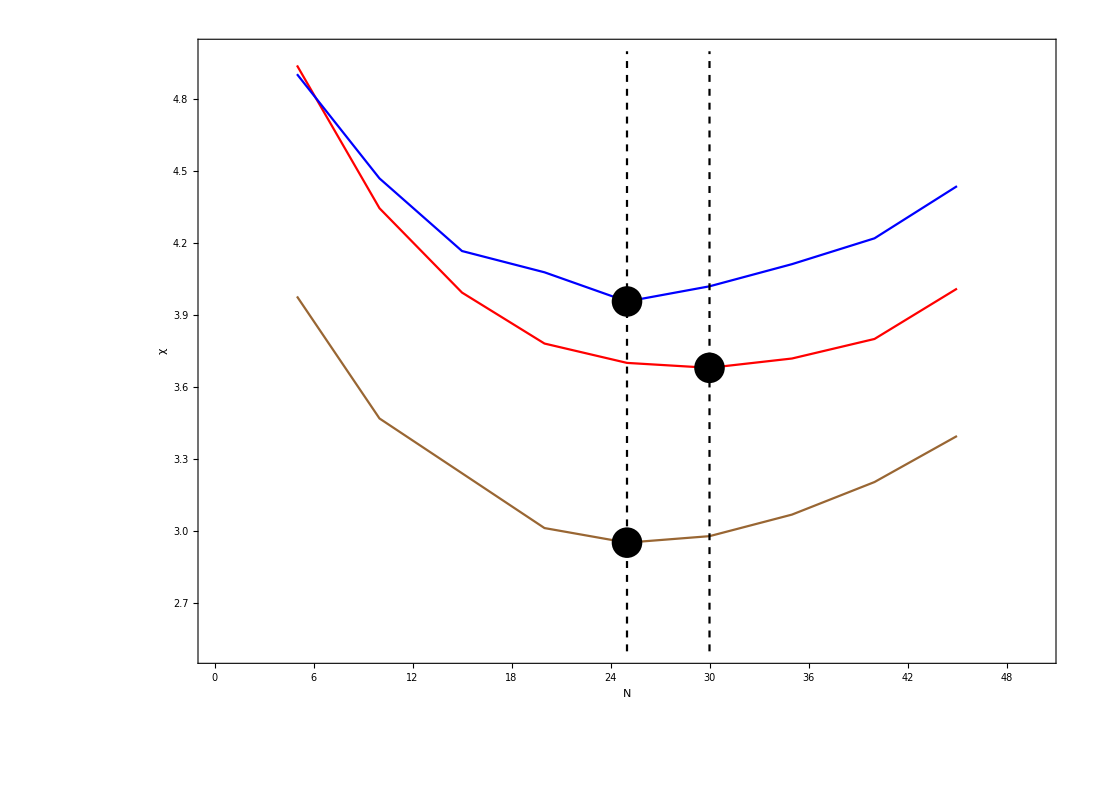

```mathematica
Show[Show[%136,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",55,GrayLevel[0.1]},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],ImageSize->Large],ImageSize->{1100,785},AspectRatio->Full]
```

```mathematica
Export["~/PhD/quantum_sudoq/fig_2_b.pdf",Show[Show[%136,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",50,GrayLevel[0.1]},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],ImageSize->Large],ImageSize->{1100,785},AspectRatio->Full]]
```

~/PhD/quantum_sudoq/fig_2_b.pdf

```mathematica
Transpose[Join[{Range[5,45,5]},{1000*%92[[7]]}]]
```

{{5,4.94089},{10,4.3459},{15,3.99461},{20,3.78224},{25,3.70164},{30,3.68109},{35,3.71994},{40,3.80136},{45,4.01101}}

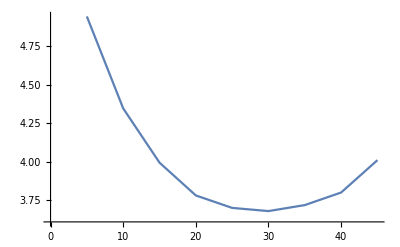

```mathematica
ListPlot[{{5,4.940891961564797},{10,4.345900317770791},{15,3.9946078996392025},{20,3.782239088279934},{25,3.7016431155340683},{30,3.6810863914747256},{35,3.719935314320688},{40,3.801356625335802},{45,4.011014881097233}},Joined->True]
```

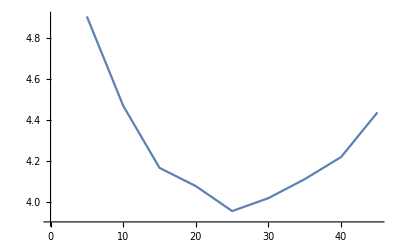

```mathematica
ListPlot[{{5,4.904517857633756},{10,4.470250466726267},{15,4.167709259106818},{20,4.079072457716857},{25,3.957528778592429},{30,4.020672216824663},{35,4.113051958756657},{40,4.220662914032613},{45,4.4379575103301265}},Joined->True]
```

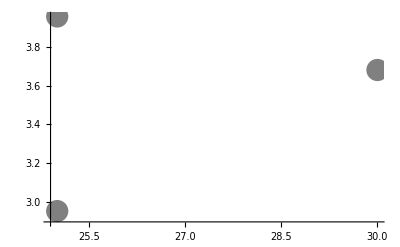

```mathematica
ListPlot[{Transpose[Join[{Range[5,45,5]},{1000*%92[[7]]}]][[6]],Transpose[Join[{Range[5,45,5]},{1000*%92[[10]]}]][[5]],Transpose[Join[{Range[5,45,5]},{1000*%92[[9]]}]][[5]]},PlotStyle->Directive[Gray,PointSize[0.04]]]
```

```mathematica
ll[X_]:=ParallelTable[b12[X+delta,X,1],{delta,Range[0.2,6-X-0.01,0.4]}]
```